```mathematica
c1=Cos[ϕ]^2/q1^2 + Sin[ϕ]^2/q2^2;
c2=Cos[ϕ]^2/q2^2 + Sin[ϕ]^2/q1^2;
c3=2 Sin[ϕ] Cos[ϕ] (1/q1^2 - 1/q2^2);
Φ[x_,y_,z_]:=-Md / Sqrt[x^2+y^2 + (a + Sqrt[z^2+b^2])^2]+-Ms / (Sqrt[x^2+y^2+z^2]+c)+vhalo Log[c1 x^2 + c2 y^2 + c3 x y + (z/qz)^2 +rh^2];

Hamiltonian[x_,y_,z_,vx_,vy_,vz_]:=(vx^2+vy^2+vz^2)/2 + Φ[x,y,z];
DHamiltonian[x_,y_,z_,vx_,vy_,vz_]:=(vx^2+vy^2+vz^2)/2 - Φ[x,y,z];
F[{x_,y_,z_,vx_,vy_,vz_}]:=D[DHamiltonian[x,y,z,vx,vy,vz],{{vx,vy,vz,x,y,z}}];
Jac[x_,y_,z_,vx_,vy_,vz_,t_]:=Outer[D,F[{x,y,z,vx,vy,vz}],{x,y,z,vx,vy,vz}]
eqns={x'[t]==F[{x[t],y[t],z[t],vx[t],vy[t],vz[t]}][[1]],y'[t]==F[{x[t],y[t],z[t],vx[t],vy[t],vz[t]}][[2]],z'[t]==F[{x[t],y[t],z[t],vx[t],vy[t],vz[t]}][[3]],vx'[t]==F[{x[t],y[t],z[t],vx[t],vy[t],vz[t]}][[4]],vy'[t]==F[{x[t],y[t],z[t],vx[t],vy[t],vz[t]}][[5]],vz'[t]==F[{x[t],y[t],z[t],vx[t],vy[t],vz[t]}][[6]]};
vhalo=Abs[-(((8 Md)/((64+(a+√(b^2))^2)^(3/2))+Ms/(8+c)^2) (rh^2+64 (Cos[ϕ]^2/q1^2+Sin[ϕ]^2/q2^2)))/(16 (Cos[ϕ]^2/q1^2+Sin[ϕ]^2/q2^2))];
Munit=2.325*10^7; Tunit=97.544;
```

```mathematica
-D[Φ[x,y,z],z] // FullSimplify
```

z (-(2 vhalo)/(qz^2 (rh^2+c1 x^2+c3 x y+c2 y^2)+z^2)-Ms/(√(x^2+y^2+z^2) (c+√(x^2+y^2+z^2))^2)-(Md (a+√(b^2+z^2)))/(√(b^2+z^2) (x^2+y^2+(a+√(b^2+z^2))^2)^(3/2)))

```mathematica
Md=10^11/Munit; Ms=3.4*10^10/Munit; a=6.5; b=.26; c=.7;rh=12;
```

```mathematica
Remove[t]
```

```mathematica
Clear[qz,q1];
```

```mathematica
Remove[x,y,z,t]
```

```mathematica
Clear[Md,Ms,a,b,c,rh,q1,q2,qz,ϕ,vhalo];
```

```mathematica
sol[{x0_,y0_,z0_,vx0_,vy0_,vz0_}]:=NDSolve[{eqns,x[0]==x0,y[0]==y0,z[0]==z0,vx[0]==vx0,vy[0]==vy0,vz[0]==vz0},{x,y,z,vx,vy,vz},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,MaxSteps->Infinity]
```

```mathematica
ϕ=Pi*.5;q1=1.4;q2=1.;qz=1.25; tend=100;
psol=sol[{30,0,0,-5,10,0}]
NIntegrate[Evaluate[Hamiltonian[x[t],y[t],z[t],vx[t],vy[t],vz[t]]]/Hamiltonian[x[0],y[0],z[0],vx[0],vy[0],vz[0]]/. psol,{t,0,tend}]/tend
Evaluate[Hamiltonian[x[0],y[0],z[0],vx[0],vy[0],vz[0]]]/.psol
ParametricPlot[Evaluate[{y[t],vy[t]}]/.psol,{t,0,tend},PlotStyle->Directive[Hue[0.67,0.6,0.6],Dotted],AspectRatio->1/2,PlotRange->Full,Frame->True,Axes->False]
```

sol[{30,0,0,-5,10,0}]

ReplaceAll::reps: {sol[{30, 0, 0, -5, 10, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 640.493\ Log[144 + 1.\ Power[« 2 »] - 5.99827×10^-17\ x[« 1 »]\ y[« 1 »] + 0.510204\ Power[« 2 »] + 0.64\ Power[« 2 »]] + 1/2\ (vx[t]^2 + vy[t]^2 + vz[t]^2) - 1462.37/0.7  + √Plus[« 3 »] - 4301.08/√x[« 1 »]^2 + y[« 1 »]^2 + Plus[« 2 »]^2/640.493\ Log[144 + Times[« 2 »] + Times[« 3 »] + Times[« 2 »] + Times[« 2 »]] + 1/2\ (vx[« 1 »]^2 + vy[« 1 »]^2 + vz[« 1 »]^2) - 1462.37/0.7  + Power[« 2 »] - 4301.08/√Power[« 2 »] + Power[« 2 »] + Power[« 2 »]/. sol[{30, 0, 0, -5, 10, 0}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 100}}.

ReplaceAll::reps: {sol[{30, 0, 0, -5, 10, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 640.493\ Log[144 + 1.\ Power[« 2 »] - 5.99827×10^-17\ x[« 1 »]\ y[« 1 »] + 0.510204\ Power[« 2 »] + 0.64\ Power[« 2 »]] + 1/2\ (vx[t]^2 + vy[t]^2 + vz[t]^2) - 1462.37/0.7  + √Plus[« 3 »] - 4301.08/√x[« 1 »]^2 + y[« 1 »]^2 + Plus[« 2 »]^2/640.493\ Log[144 + Times[« 2 »] + Times[« 3 »] + Times[« 2 »] + Times[« 2 »]] + 1/2\ (vx[« 1 »]^2 + vy[« 1 »]^2 + vz[« 1 »]^2) - 1462.37/0.7  + Power[« 2 »] - 4301.08/√Power[« 2 »] + Power[« 2 »] + Power[« 2 »]/. sol[{30, 0, 0, -5, 10, 0}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 100}}.

1/100 NIntegrate[Evaluate[Hamiltonian[x[t],y[t],z[t],vx[t],vy[t],vz[t]]]/Hamiltonian[x[0],y[0],z[0],vx[0],vy[0],vz[0]]/.psol,{t,0,tend}]

ReplaceAll::reps: {sol[{30, 0, 0, -5, 10, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

640.493 Log[144+1. x[0]^2-5.99827×10^-17 x[0] y[0]+0.510204 y[0]^2+0.64 z[0]^2]+1/2 (vx[0]^2+vy[0]^2+vz[0]^2)-1462.37/(0.7+√(x[0]^2+y[0]^2+z[0]^2))-4301.08/(√(x[0]^2+y[0]^2+(6.5+√(0.0676+z[0]^2))^2))/.sol[{30,0,0,-5,10,0}]

ReplaceAll::reps: {sol[{30, 0, 0, -5, 10, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[{30., 0., 0., -5., 10., 0.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[{30, 0, 0, -5, 10, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

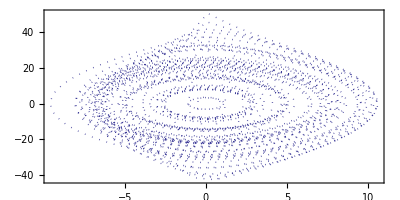

{1.}

```mathematica
ParametricPlot[Evaluate[{x[t],vx[t]}]/.psol,{t,0,tend},PlotStyle->Directive[Hue[0.67,0.6,0.6],Dotted],AspectRatio->1/2,PlotRange->Full,Frame->True,Axes->False]
```

```mathematica
Remove[x,y,z]
```

```mathematica
psecty[{x0_,y0_,z0_,vx0_,vy0_,vz0_}]:=Reap[NDSolve[{eqns,x[0]==x0,y[0]==y0,z[0]==z0,vx[0]==vx0,vy[0]==vy0,vz[0]==vz0,WhenEvent[y[t]>0,Sow[{x[t],vx[t]}]]},{},{t,0,1000},MaxSteps->∞]][[-1,1]]
```

```mathematica
dat=Map[psect,{{8,0,0,1.1,-.3,0},{1,0,0,1.1,47.7914813544228,0},{1,0,0,1.1,39.77450464034727,0},{1,0,0,1.1,34.49023122494788,0},{8,0,0,1.1401754250992178,0,0},{7,0,0,8,11.810834508800216,0}}];
```

```mathematica
Energy[x_]:=Hamiltonian[x[[1]],x[[2]],x[[3]],x[[4]],x[[5]],x[[6]],0]
```

```mathematica
E0=Energy[{30,0,0,-5,10,0}]
```

4326.95

```mathematica
NSolve[Energy[{-12,0,0,-3,x,0}]==E0,x]
```

{{x→-47.3876},{x→47.3876}}

```mathematica
ListPlot[dat,Frame->True,Axes->False,FrameLabel->{"x","v_x"}]
```

-Graphics-

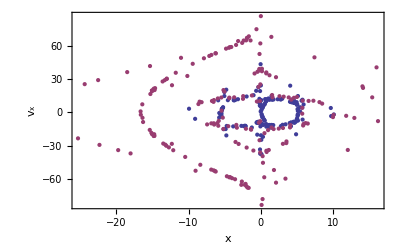

```mathematica
dat2=Map[psecty,{(*{30,0,0,-5,10,0},{10,0,0,8,-11.810834508800216,0},{15,0,0,8,-41.56175990402763,0},*){.1,0,0,0,84.94607747341651,0},(*{20,0,0,31.460944991097527,-12,0},{-5,0,0,0,60.15608680575502,0},{5,0,0,0,60.15608680575502,0},{-10,0,0,30,41.208072073829406,0},{-18,0,0,0,37.169773293256206,0},*){.05,0,0,-20,84.02222797509768,0}(*,{-11,0,0,1,49.20958253157236,0},{-8,0,0,-40,37.06859825007528,0},{-1,0,0,-2,72.4845960620298,0},{1,0,0,-2,72.4845960620298,0},{-14,0,0,1.5,44.01284351850099,0},{-12,0,0,-3,-47.38762896577727,0}*)}];
ListPlot[dat2,Frame->True,Axes->False,FrameLabel->{"x","v_x"}]
```

```mathematica
Clear[q1]
```

```mathematica
ϕ=Pi/2;q1=1.6;q2=1;qz=1.25;
```

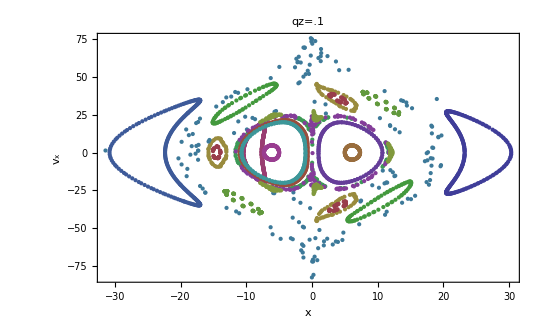

```mathematica
dat2pi=Map[psecty,dat2Inits]; ListPlot[dat2pi,Frame->True,Axes->False,FrameLabel->{"x","v_x"},PlotLabel->"qz=.1",PlotRange->Full]
```

```mathematica
dat2Inits={{30,0,0,-5,10,0},{10,0,0,8,-11.810834508800216,0},{15,0,0,8,-41.56175990402763,0},{.1,0,0,0,84.94607747341651,0},{20,0,0,31.460944991097527,-12,0},{-5,0,0,0,60.15608680575502,0},{5,0,0,0,60.15608680575502,0},{-10,0,0,30,41.208072073829406,0},{-18,0,0,0,37.169773293256206,0},{.05,0,0,-20,84.02222797509768,0},{-11,0,0,1,49.20958253157236,0},{-8,0,0,-40,37.06859825007528,0},{-1,0,0,-2,72.4845960620298,0},{1,0,0,-2,72.4845960620298,0},{-14,0,0,1.5,44.01284351850099,0},{-12,0,0,-3,-47.38762896577727,0}}
```

{{30,0,0,-5,10,0},{10,0,0,8,-11.8108,0},{15,0,0,8,-41.5618,0},{0.1,0,0,0,84.9461,0},{20,0,0,31.4609,-12,0},{-5,0,0,0,60.1561,0},{5,0,0,0,60.1561,0},{-10,0,0,30,41.2081,0},{-18,0,0,0,37.1698,0},{0.05,0,0,-20,84.0222,0},{-11,0,0,1,49.2096,0},{-8,0,0,-40,37.0686,0},{-1,0,0,-2,72.4846,0},{1,0,0,-2,72.4846,0},{-14,0,0,1.5,44.0128,0},{-12,0,0,-3,-47.3876,0}}

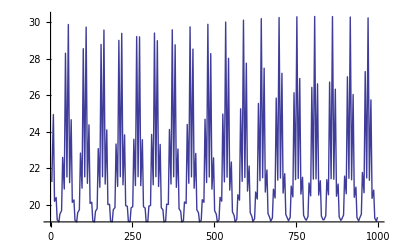

```mathematica
ListPlot[dat21[[1]][[All,{3,1}]],Joined->True]
ListPlot[Abs[Fourier[dat21[[1]][[All,{3,1}]]]]^2,Joined->True]
```

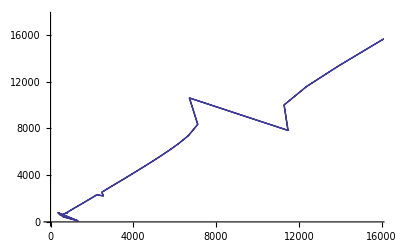

{4.76379,3.41017,5.05709,3.16049,5.16269,3.12111,5.12166,3.27294,4.91695,3.67081,4.48905,4.26829,3.88682,4.78321,3.39231,5.06591,3.15429,5.16397,3.12379,5.11595,3.28592,4.90197,3.6965,4.46255,4.29733,3.85817,4.80204,3.37509,5.07432,3.14856,5.16492,3.1269,5.10986,3.29948,4.88644,3.72271,4.43559,4.32611,3.82984,4.82031,3.3585,5.08232,3.14328,5.16555,3.13044,5.10339,3.31365,4.87037,3.74942,4.40819,4.35459,3.80187,4.83801,3.34253,5.08992,3.13845,5.16586,3.13441,5.09653,3.32844,4.85373,3.77659,4.38038,4.38273,3.77429,4.85515,3.32717,5.09712,3.13406,5.16584,3.13883,5.08929,3.34384,4.83653,3.8042,4.3522,4.41051,3.74714,4.87174,3.31243,5.10394,3.13011,5.1655,3.1437,5.08164,3.35987,4.81876,3.83222,4.32366,4.43789,3.72044,4.88778,3.29828,5.11037,3.1266,5.16483,3.14902,5.07359,3.37654,4.80041,3.86062,4.2948,4.46485,3.69422,4.90328,3.28474,5.11644,3.12352,5.16384,3.1548,5.06512,3.39385,4.78147,3.88937,4.26566,4.49137,3.6685,4.91825,3.27177,5.12213,3.12086,5.16252,3.16105,5.05622,3.4118,4.76195,3.91841,4.23627,4.51742,3.64331,4.93269,3.25939,5.12745,3.11863,5.16087,3.16778,5.04689,3.43041,4.74183,3.94773,4.20666,4.54299,3.61867,4.94662,3.24757,5.13241,3.11681,5.15889,3.175,5.03712,3.44967,4.72111,3.97728,4.17689,4.56805,3.59459,4.96004,3.23632,5.13702,3.11542,5.15657,3.18272,5.0269,3.46959,4.6998,4.00701,4.14698,4.59258,3.5711,4.97296,3.22561,5.14127,3.11444,5.15392,3.19095,5.01621,3.49015,4.67789,4.03689,4.11699,4.61658,3.54821,4.98539,3.21545,5.14518,3.11388,5.15093,3.19969,5.00506,3.51137,4.65539,4.06687,4.08695,4.64002,3.52592,4.99733,3.20582,5.14874,3.11374,5.14759,3.20895,4.99343,3.53323,4.63231,4.0969,4.05692,4.66291,3.50426,5.0088,3.19672,5.15195,3.11401,5.14391,3.21875,4.98131,3.55573,4.60866,4.12694,4.02694,4.68522,3.48323,5.0198,3.18814,5.15482,3.11471,5.13988,3.2291,4.96869,3.57885,4.58444,4.15695,3.99705,4.70696,3.46284,5.03034,3.18006,5.15736,3.11582}

```mathematica
J
Differences[dat21[[1]][[All,3]]]
```

```mathematica
psectz[{x0_,y0_,z0_,vx0_,vy0_,vz0_}]:=Reap[NDSolve[{eqns,x[0]==x0,y[0]==y0,z[0]==z0,vx[0]==vx0,vy[0]==vy0,vz[0]==vz0,WhenEvent[z[t]>0 ,Sow[{x[t],vx[t]}]]},{},{t,0,1000},MaxSteps->∞]][[-1,1]]
```

```mathematica
dat3=Map[psectz,{{30,0,0,-5,0,10},{10,0,0,8,0,-11.810834508800216},{15,0,0,8,0,-41.56175990402763},{.1,0,0,0,0,84.94607747341651},{20,0,0,31.460944991097527,0,-12},{-5,0,0,0,0,60.15608680575502},{5,0,0,0,0,60.15608680575502},{-10,0,0,30,0,41.208072073829406},{-18,0,0,0,0,37.169773293256206},{.05,0,0,-20,0,84.02222797509768},{-11,0,0,1,0,49.20958253157236},{-8,0,0,-40,0,37.06859825007528},{-1,0,0,-2,0,72.4845960620298},{1,0,0,-2,0,72.4845960620298},{-14,0,0,1.5,0,44.01284351850099},{-12,0,0,-3,0,-47.38762896577727}}];
ListPlot[dat3,Frame->True,Axes->False,FrameLabel->{"x","v_x"}]
```

```mathematica
dat3Inits={{30,0,0,-5,0,10},{10,0,0,8,0,-11.810834508800216},{15,0,0,8,0,-41.56175990402763},{.1,0,0,0,0,84.94607747341651},{20,0,0,31.460944991097527,0,-12},{-5,0,0,0,0,60.15608680575502},{5,0,0,0,0,60.15608680575502},{-10,0,0,30,0,41.208072073829406},{-18,0,0,0,0,37.169773293256206},{.05,0,0,-20,0,84.02222797509768},{-11,0,0,1,0,49.20958253157236},{-8,0,0,-40,0,37.06859825007528},{-1,0,0,-2,0,72.4845960620298},{1,0,0,-2,0,72.4845960620298},{-14,0,0,1.5,0,44.01284351850099},{-12,0,0,-3,0,-47.38762896577727}}

dat3Inits[[1]]
```

{{30,0,0,-5,0,10},{10,0,0,8,0,-11.8108},{15,0,0,8,0,-41.5618},{0.1,0,0,0,0,84.9461},{20,0,0,31.4609,0,-12},{-5,0,0,0,0,60.1561},{5,0,0,0,0,60.1561},{-10,0,0,30,0,41.2081},{-18,0,0,0,0,37.1698},{0.05,0,0,-20,0,84.0222},{-11,0,0,1,0,49.2096},{-8,0,0,-40,0,37.0686},{-1,0,0,-2,0,72.4846},{1,0,0,-2,0,72.4846},{-14,0,0,1.5,0,44.0128},{-12,0,0,-3,0,-47.3876}}

{30,0,0,-5,0,10}

```mathematica
psectx[{x0_,y0_,z0_,vx0_,vy0_,vz0_}]:=Reap[NDSolve[{eqns,x[0]==x0,y[0]==y0,z[0]==z0,vx[0]==vx0,vy[0]==vy0,vz[0]==vz0,WhenEvent[x[t]>0 ,Sow[{y[t],vy[t]}]]},{},{t,0,1000},MaxSteps->∞]][[-1,1]]
```

```mathematica
dat4=Map[psectx,{{30,0,0,-5,0,10},{10,0,0,8,0,-11.810834508800216},{15,0,0,8,0,-41.56175990402763},{.1,0,0,0,0,84.94607747341651},{20,0,0,31.460944991097527,0,-12},{-5,0,0,0,0,60.15608680575502},{5,0,0,0,0,60.15608680575502},{-10,0,0,30,0,41.208072073829406},{-18,0,0,0,0,37.169773293256206},{.05,0,0,-20,0,84.02222797509768},{-11,0,0,1,0,49.20958253157236},{-8,0,0,-40,0,37.06859825007528},{-1,0,0,-2,0,72.4845960620298},{1,0,0,-2,0,72.4845960620298},{-14,0,0,1.5,0,44.01284351850099},{-12,0,0,-3,0,-47.38762896577727}}];
```

{{30,0,0,-5,0,10},{10,0,0,8,0,-11.8108},{15,0,0,8,0,-41.5618},{0.1,0,0,0,0,84.9461},{20,0,0,31.4609,0,-12},{-5,0,0,0,0,60.1561},{5,0,0,0,0,60.1561},{-10,0,0,30,0,41.2081},{-18,0,0,0,0,37.1698},{0.05,0,0,-20,0,84.0222},{-11,0,0,1,0,49.2096},{-8,0,0,-40,0,37.0686},{-1,0,0,-2,0,72.4846},{1,0,0,-2,0,72.4846},{-14,0,0,1.5,0,44.0128},{-12,0,0,-3,0,-47.3876}}

```mathematica
Table[Energy[ICs[[i]]],{i,1,16}]
```

{4326.95,3129.65,4326.95,4326.95,4326.95,4326.95,4326.95,4326.95,4326.95,4326.95,4326.95,4326.95,4326.95,4326.95,4326.95,4326.95}

```mathematica
{{30,0,0,-5,0,10},{10,0,0,8,0,-11.810834508800216},{15,0,0,8,0,-41.56175990402763},{0.1,0,0,0,0,84.94607747341651},{20,0,0,31.460944991097527,0,-12},{-5,0,0,0,0,60.15608680575502},{5,0,0,0,0,60.15608680575502},{-10,0,0,30,0,41.208072073829406},{-18,0,0,0,0,37.169773293256206},{0.05,0,0,-20,0,84.02222797509768},{-11,0,0,1,0,49.20958253157236},{-8,0,0,-40,0,37.06859825007528},{-1,0,0,-2,0,72.4845960620298},{1,0,0,-2,0,72.4845960620298},{-14,0,0,1.5,0,44.01284351850099},{-12,0,0,-3,0,-47.38762896577727}}[1]
```

```mathematica
pow2=Abs[Fourier[dat2[[1]]]]^2
```

{{58103.5,57922.1},{0.0610221,0.386822},{0.0653725,0.391492},{0.0731697,0.399871},{0.0852033,0.412719},{0.102816,0.431408},{0.128079,0.458022},{0.164263,0.495896},{0.216488,0.550185},{0.293102,0.62932},{0.408162,0.747478},{0.58666,0.929826},{0.875762,1.22382},{1.3723,1.7268},{2.29868,2.66214},{4.25343,4.63043},{9.29968,9.70024},{28.58,29.0352},{271.564,272.227},{360.721,360.665},{41.9923,42.1926},{16.5845,16.8387},{9.32587,9.60396},{6.21843,6.51067},{4.58338,4.88527},{3.60765,3.91677},{2.97403,3.28881},{2.53688,2.85621},{2.22139,2.54432},{1.98563,2.31118},{1.80465,2.13171},{1.66269,1.98967},{1.54945,1.87394},{1.45794,1.77567},{1.38342,1.68585},{1.32312,1.5887},{1.2873,1.41893},{7.0964,1.44375},{1.20272,1.90449},{1.1642,1.7297},{1.13776,1.66538},{1.11673,1.63046},{1.09972,1.60941},{1.0861,1.59697},{1.07536,1.59077},{1.06714,1.58961},{1.06112,1.59276},{1.05698,1.59986},{1.0544,1.61073},{1.05295,1.62542},{1.05207,1.64424},{1.05074,1.66797},{1.04687,1.69841},{1.03488,1.7402},{0.990329,1.80872},{0.929097,2.11177},{1.56886,1.32968},{1.29074,1.64776},{1.25853,1.73602},{1.25795,1.79606},{1.269,1.8489},{1.28651,1.90023},{1.30861,1.95231},{1.33458,2.0062},{1.36415,2.06255},{1.39735,2.12166},{1.43445,2.18367},{1.47598,2.24847},{1.52292,2.31537},{1.57714,2.38269},{1.6428,2.44596},{1.73163,2.49173},{1.89646,2.46146},{3.65035,1.47384},{1.45395,3.57126},{1.69972,3.36486},{1.81733,3.43694},{1.91581,3.56517},{2.01028,3.72599},{2.10588,3.91416},{2.2049,4.12999},{2.30845,4.37644},{2.41695,4.65884},{2.53013,4.98505},{2.64681,5.36702},{2.7642,5.82306},{2.87673,6.38368},{2.9733,7.10417},{3.03164,8.09985},{3.00707,9.66515},{2.8397,12.8674},{4.02338,26.6094},{68.7413,15.7415},{13.1061,2.54071},{10.411,5.22141},{10.1127,7.12818},{10.54,8.83057},{11.397,10.5823},{12.6385,12.5434},{14.3144,14.865},{16.5473,17.7313},{19.5517,21.4066},{23.6888,26.3025},{29.5897,33.1145},{38.4225,43.1069},{52.5548,58.8094},{77.4017,85.9472},{127.785,140.03},{257.699,276.969},{811.031,848.745},{21010.6,21221.8},{2003.48,1931.92},{362.626,329.306},{143.861,120.939},{76.3579,58.1832},{47.6593,32.1172},{33.3125,19.3635},{25.5737,12.6104},{21.4323,9.04826},{19.608,7.4933},{19.608,7.4933},{21.4323,9.04826},{25.5737,12.6104},{33.3125,19.3635},{47.6593,32.1172},{76.3579,58.1832},{143.861,120.939},{362.626,329.306},{2003.48,1931.92},{21010.6,21221.8},{811.031,848.745},{257.699,276.969},{127.785,140.03},{77.4017,85.9472},{52.5548,58.8094},{38.4225,43.1069},{29.5897,33.1145},{23.6888,26.3025},{19.5517,21.4066},{16.5473,17.7313},{14.3144,14.865},{12.6385,12.5434},{11.397,10.5823},{10.54,8.83057},{10.1127,7.12818},{10.411,5.22141},{13.1061,2.54071},{68.7413,15.7415},{4.02338,26.6094},{2.8397,12.8674},{3.00707,9.66515},{3.03164,8.09985},{2.9733,7.10417},{2.87673,6.38368},{2.7642,5.82306},{2.64681,5.36702},{2.53013,4.98505},{2.41695,4.65884},{2.30845,4.37644},{2.2049,4.12999},{2.10588,3.91416},{2.01028,3.72599},{1.91581,3.56517},{1.81733,3.43694},{1.69972,3.36486},{1.45395,3.57126},{3.65035,1.47384},{1.89646,2.46146},{1.73163,2.49173},{1.6428,2.44596},{1.57714,2.38269},{1.52292,2.31537},{1.47598,2.24847},{1.43445,2.18367},{1.39735,2.12166},{1.36415,2.06255},{1.33458,2.0062},{1.30861,1.95231},{1.28651,1.90023},{1.269,1.8489},{1.25795,1.79606},{1.25853,1.73602},{1.29074,1.64776},{1.56886,1.32968},{0.929097,2.11177},{0.990329,1.80872},{1.03488,1.7402},{1.04687,1.69841},{1.05074,1.66797},{1.05207,1.64424},{1.05295,1.62542},{1.0544,1.61073},{1.05698,1.59986},{1.06112,1.59276},{1.06714,1.58961},{1.07536,1.59077},{1.0861,1.59697},{1.09972,1.60941},{1.11673,1.63046},{1.13776,1.66538},{1.1642,1.7297},{1.20272,1.90449},{7.0964,1.44375},{1.2873,1.41893},{1.32312,1.5887},{1.38342,1.68585},{1.45794,1.77567},{1.54945,1.87394},{1.66269,1.98967},{1.80465,2.13171},{1.98563,2.31118},{2.22139,2.54432},{2.53688,2.85621},{2.97403,3.28881},{3.60765,3.91677},{4.58338,4.88527},{6.21843,6.51067},{9.32587,9.60396},{16.5845,16.8387},{41.9923,42.1926},{360.721,360.665},{271.564,272.227},{28.58,29.0352},{9.29968,9.70024},{4.25343,4.63043},{2.29868,2.66214},{1.3723,1.7268},{0.875762,1.22382},{0.58666,0.929826},{0.408162,0.747478},{0.293102,0.62932},{0.216488,0.550185},{0.164263,0.495896},{0.128079,0.458022},{0.102816,0.431408},{0.0852033,0.412719},{0.0731697,0.399871},{0.0653725,0.391492},{0.0610221,0.386822}}

```mathematica
ListPlot[dat2[[1]][[All,1]]]
```

```mathematica
ListPlot[dat2[[1]]]
```

```mathematica
JacobianMatrix[F[x,y,z,vx,vy,vz,t],{x,y,z,vx,vy,vz}]
```

JacobianMatrix[{vx,vy,vz,-(640.493 (2. x-6.80359×10^-17 y))/(144+1. x^2-6.80359×10^-17 x y+0.444444 y^2+0.64 z^2)-(1462.37 x)/(√(x^2+y^2+z^2) (0.7+√(x^2+y^2+z^2))^2)-(4301.08 x)/((x^2+y^2+(6.5+√(0.0676+z^2))^2)^(3/2)),-(640.493 (-6.80359×10^-17 x+0.888889 y))/(144+1. x^2-6.80359×10^-17 x y+0.444444 y^2+0.64 z^2)-(1462.37 y)/(√(x^2+y^2+z^2) (0.7+√(x^2+y^2+z^2))^2)-(4301.08 y)/((x^2+y^2+(6.5+√(0.0676+z^2))^2)^(3/2)),-(819.831 z)/(144+1. x^2-6.80359×10^-17 x y+0.444444 y^2+0.64 z^2)-(1462.37 z)/(√(x^2+y^2+z^2) (0.7+√(x^2+y^2+z^2))^2)-(4301.08 z (6.5+√(0.0676+z^2)))/(√(0.0676+z^2) (x^2+y^2+(6.5+√(0.0676+z^2))^2)^(3/2))},{x,y,z,vx,vy,vz}]

```mathematica
Clear[x,y,z]
```

```mathematica
D[JacobianDeterminant[F,{x,y,z,vx,vy,vz,t}], vx]
```

JacobianDeterminant^(0,{0,0,0,1,0,0,0})[F,{x,y,z,vx,vy,vz,t}]

```mathematica
Series[Derivative[0,{0,0,0,1,0,0,0}][JacobianDeterminant][F,{x,y,z,vx,vy,vz,t}],{F,0,4}]
```

JacobianDeterminant^(0,{0,0,0,1,0,0,0})[0,{x,y,z,vx,vy,vz,t}]+JacobianDeterminant^(1,{0,0,0,1,0,0,0})[0,{x,y,z,vx,vy,vz,t}] F+1/2 JacobianDeterminant^(2,{0,0,0,1,0,0,0})[0,{x,y,z,vx,vy,vz,t}] F^2+1/6 JacobianDeterminant^(3,{0,0,0,1,0,0,0})[0,{x,y,z,vx,vy,vz,t}] F^3+1/24 JacobianDeterminant^(4,{0,0,0,1,0,0,0})[0,{x,y,z,vx,vy,vz,t}] F^4+O[F]^5

```mathematica
Det[Jac[x,y,z,vx,vy,vz,t]] // Simplify
```

$Aborted

```mathematica
Import["~/Dropbox/chaos/lce.m"]
```

```mathematica
?LCEsC
```

LCEsC[flist, x0, T, K, TR, stepsize, opts] computes the Lyapunov spectrum and
dimension of a given continuous-time dynamical system flist with starting initial
condition x0, for T seconds and K steps, excluding the transient for TR steps. If
LCEsPlot -> True option is specified, then LCEsC plots the entire spectrum.

```mathematica
lam=LCEsC[F[x,y,z,vx,vy,vz,t],{x,y,z,vx,vy,vz},.2,2,1,.0001,LCEsPlot->True]
```

$Aborted

```mathematica
x
```

x

```mathematica
listsol[{x0_,y0_,z0_,vx0_,vy0_,vz0_}]:=Reap[NDSolve[{eqns,x[0]==x0,y[0]==y0,z[0]==z0,vx[0]==vx0,vy[0]==vy0,vz[0]==vz0},{x,y,z,vx,vy,vz},{t,0,tend},StepMonitor:>Sow[{t,x[t],y[t],z[t],vx[t],vy[t],vz[t]}],AccuracyGoal->10,PrecisionGoal->10,MaxSteps->Infinity]]
```

```mathematica
sol1=sol[{15,0,0,8,0,-41.56175990402763}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>],z→InterpolatingFunction[{{0.,100.}},<>],vx→InterpolatingFunction[{{0.,100.}},<>],vy→InterpolatingFunction[{{0.,100.}},<>],vz→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
Plot[Evaluate[sol1[[1,1]][t],{t,0,100}],{t,0,100}]
```

Plot::nonopt: Options expected (instead of {t, 0, 100}) beyond position 3 in (x → TagBox[« 1 », False, Rule[Editable, False]])[t], {t, 0, 100}, {t, 0, 100}. An option must be a rule or a list of rules.

Plot[(x→InterpolatingFunction[{{0.,100.}},<>])[t],{t,0,100},{t,0,100}]

```mathematica
.
```

```mathematica
Plot[Abs[Fourier[Evaluate[x[t] /. sol1[[1,1]]]]]^2,{t,0,100}]
```

Fourier::fftl: Argument 0.0960893 is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument -1.20467 is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument -9.35293 is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

-Graphics-

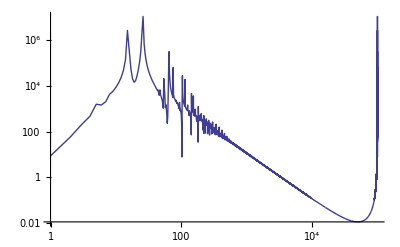

```mathematica
ListLogLogPlot[Abs[Fourier[Table[Evaluate[vz[t] /. sol1[[1,6]]],{t,0,100,.001}]]]^2,Joined->True,PlotRange->Full]
```

```mathematica
Table[{x[t],y[t],z[t],vx[t],vy[t],vz[t]}[[i]]==F[x[t],y[t],z[t],vx[t],vy[t],vz[t],t][[i]],{i,1,6}]
```

{x[t]==vx[t],y[t]==vy[t],z[t]==vz[t],vx[t]==-(640.493 (2. x[t]-6.80359×10^-17 y[t]))/(144+1. x[t]^2-6.80359×10^-17 x[t] y[t]+0.444444 y[t]^2+0.64 z[t]^2)-(1462.37 x[t])/(√(x[t]^2+y[t]^2+z[t]^2) (0.7+√(x[t]^2+y[t]^2+z[t]^2))^2)-(4301.08 x[t])/((x[t]^2+y[t]^2+(6.5+√(0.0676+z[t]^2))^2)^(3/2)),vy[t]==-(640.493 (-6.80359×10^-17 x[t]+0.888889 y[t]))/(144+1. x[t]^2-6.80359×10^-17 x[t] y[t]+0.444444 y[t]^2+0.64 z[t]^2)-(1462.37 y[t])/(√(x[t]^2+y[t]^2+z[t]^2) (0.7+√(x[t]^2+y[t]^2+z[t]^2))^2)-(4301.08 y[t])/((x[t]^2+y[t]^2+(6.5+√(0.0676+z[t]^2))^2)^(3/2)),vz[t]==-(819.831 z[t])/(144+1. x[t]^2-6.80359×10^-17 x[t] y[t]+0.444444 y[t]^2+0.64 z[t]^2)-(1462.37 z[t])/(√(x[t]^2+y[t]^2+z[t]^2) (0.7+√(x[t]^2+y[t]^2+z[t]^2))^2)-(4301.08 z[t] (6.5+√(0.0676+z[t]^2)))/(√(0.0676+z[t]^2) (x[t]^2+y[t]^2+(6.5+√(0.0676+z[t]^2))^2)^(3/2))}

```mathematica
Table[Evaluate[input/. sol1],{t,0,100,1}]
```

{{{15.,0.,0.,8.,0.,-41.5618}},{{-0.650466,5.62213×10^-16,-27.3446,-26.6321,6.81899×10^-16,-7.77856}},{{-18.9966,6.44101×10^-16,-16.9328,-3.96859,-7.12853×10^-16,25.7832}},{{3.85801,-8.53691×10^-16,12.8299,44.0402,-1.32151×10^-15,14.6404}},{{28.1684,-7.65212×10^-16,11.1839,3.92321,1.18261×10^-15,-10.9767}},{{8.92702,1.11282×10^-15,-3.72313,-49.0246,1.96354×10^-15,-13.6256}},{{-27.9805,-1.00448×10^-15,4.11413,-10.7689,-3.65431×10^-15,12.6443}},{{-17.5872,-4.39776×10^-15,12.2264,32.2458,-2.37207×10^-15,0.782772}},{{19.1486,3.1841×10^-16,-7.56663,14.1929,1.0885×10^-14,-29.5839}},{{12.716,1.00045×10^-14,-26.1134,-22.5195,7.03816×10^-15,-4.91403}},{{-13.0398,1.01321×10^-14,-10.697,-15.8228,-9.58036×10^-15,36.5381}},{{-0.204549,-6.91112×10^-15,22.956,30.2112,-1.76926×10^-14,15.6464}},{{21.2153,-1.81144×10^-14,19.6708,7.18976,-3.87529×10^-15,-18.1166}},{{4.63908,-9.5843×10^-15,-6.78429,-47.6448,3.05435×10^-14,-23.8421}},{{-28.208,2.46209×10^-14,-8.53111,-10.6555,2.71371×10^-14,8.68291}},{{-16.9894,3.78874×10^-14,3.01632,36.5151,-9.13853×10^-15,11.5096}},{{24.3984,-4.13651×10^-14,-4.94033,17.9504,-9.75224×10^-14,-16.6308}},{{21.0344,-1.10159×10^-13,-15.9281,-23.5092,-3.04361×10^-14,-3.28016}},{{-14.4379,-3.19011×10^-14,0.282541,-22.7093,2.12675×10^-13,36.8253}},{{-11.7935,1.61603×10^-13,26.509,20.1478,1.41124×10^-13,11.8845}},{{11.9172,2.03407×10^-13,19.0728,17.9297,-8.0453×10^-14,-27.4816}},{{3.48059,-2.23276×10^-14,-16.2457,-34.314,-3.1723×10^-13,-24.6998}},{{-22.8252,-2.63932×10^-13,-19.6492,-11.3013,-1.48568×10^-13,11.7493}},{{-13.2213,-2.74059×10^-13,0.735967,36.6492,2.25126×10^-13,26.5468}},{{26.3775,3.52281×10^-13,5.51726,18.2088,6.38144×10^-13,-8.39325}},{{22.7228,7.79×10^-13,-4.37459,-26.4543,1.23376×10^-13,-8.80606}},{{-19.2864,-3.20709×10^-13,3.3446,-26.0191,-2.07541×10^-12,22.3518}},{{-22.2816,-1.95644×10^-12,19.0075,16.7477,-1.04156×10^-12,7.21724}},{{8.81984,-1.58108×10^-12,9.09338,31.9838,2.65366×10^-12,-33.7068}},{{10.8928,1.96682×10^-12,-23.9268,-19.5934,3.16133×10^-12,-19.7379}},{{-12.2254,3.69857×10^-12,-24.2035,-18.2318,3.27889×10^-14,18.823}},{{-9.11495,1.38642×10^-12,7.69711,33.089,-5.22739×10^-12,33.9528}},{{23.0843,-3.85416×10^-12,17.6644,16.8207,-4.03867×10^-12,-6.82763}},{{19.8987,-5.91014×10^-12,3.07259,-26.1459,7.94955×10^-13,-20.6539}},{{-22.5293,4.73043×10^-12,-3.12286,-26.752,1.50254×10^-11,10.092}},{{-26.3113,1.58595×10^-11,7.04008,17.9354,6.05222×10^-12,7.75867}},{{12.5646,4.10827×10^-12,1.19132,36.703,-4.01455×10^-11,-28.1322}},{{21.7567,-3.17554×10^-11,-20.6824,-11.6757,-2.67353×10^-11,-12.6006}},{{-3.85851,-3.92094×10^-11,-17.6009,-32.3426,2.18439×10^-11,24.2211}},{{-11.0842,1.48491×10^-11,18.1133,19.671,6.42228×10^-11,28.6159}},{{13.3388,5.9276×10^-11,26.0996,19.4075,2.00725×10^-11,-11.194}},{{15.0264,4.7946×10^-11,1.29389,-23.0263,-5.34763×10^-11,-35.1957}},{{-21.5099,-4.99206×10^-11,-14.4563,-23.9691,-9.6046×10^-11,3.4542}},{{-24.9164,-1.15087×10^-10,-4.01347,18.0455,-2.42706×10^-11,15.3823}},{{16.587,3.43561×10^-11,2.26499,36.8279,3.38123×10^-10,-13.3732}},{{27.8638,3.03325×10^-10,-10.0974,-10.4942,1.8004×10^-10,-8.6713}},{{-4.07556,2.57712×10^-10,-7.75831,-46.6182,-5.18429×10^-10,24.2509}},{{-20.0378,-4.43294×10^-10,20.1909,8.04044,-6.11057×10^-10,19.344}},{{1.30493,-7.74068×10^-10,24.0292,28.6478,5.93848×10^-11,-15.2812}},{{12.8453,-1.26515×10^-10,-9.20298,-17.1196,1.14329×10^-9,-37.5584}},{{-14.1401,8.4743×10^-10,-25.1432,-22.436,6.41585×10^-10,4.46996}},{{-19.9054,1.05536×10^-9,-7.8021,14.8296,-3.26072×10^-10,27.7167}},{{17.6981,-4.98022×10^-10,10.8635,33.052,-2.19536×10^-9,-1.59349}},{{28.3275,-2.17847×10^-9,2.70516,-10.77,-1.01659×10^-9,-11.9345}},{{-8.35364,-7.79402×10^-10,-3.66075,-49.4431,6.73248×10^-9,15.4234}},{{-27.584,5.29573×10^-9,12.5389,3.95706,4.58514×10^-9,11.5529}},{{-3.8991,6.81605×10^-9,14.0891,42.2119,-3.87057×10^-9,-15.0698}},{{17.9831,-4.60339×10^-9,-16.739,-5.16903,-1.28103×10^-8,-27.2991}},{{-0.922756,-1.33194×10^-8,-27.9113,-25.8242,-3.17307×10^-9,7.42658}},{{-15.2579,-8.15775×10^-9,-1.54966,8.47211,1.47835×10^-8,40.7331}},{{13.4524,1.04072×10^-8,22.0383,27.6742,1.58111×10^-8,1.52859}},{{23.9329,1.98882×10^-8,11.0696,-8.73009,2.08131×10^-9,-20.5002}},{{-11.2555,-1.46534×10^-10,-7.80981,-44.5182,-4.89135×10^-8,0.480826}},{{-30.0015,-4.0856×10^-8,-0.0719113,3.75792,-2.89131×10^-8,10.5224}},{{-1.96824,-4.09525×10^-8,6.453,55.1137,6.96657×10^-8,-7.27475}},{{25.7723,8.12648×10^-8,-13.4427,1.83123,1.07415×10^-7,-16.2932}},{{9.02116,1.42589×10^-7,-19.6281,-33.8164,-8.38972×10^-9,8.11277}},{{-16.3348,-9.12904×10^-9,9.81435,1.30049,-2.44438×10^-7,35.8404}},{{1.57637,-2.03312×10^-7,28.9282,25.2278,-1.14768×10^-7,-0.0385288}},{{17.3551,-2.03871×10^-7,10.7637,-1.3074,1.30558×10^-7,-33.6538}},{{-10.4206,9.08175×10^-8,-17.5589,-35.2696,3.51779×10^-7,-7.13534}},{{-26.9071,3.48208×10^-7,-11.6392,2.90899,1.46802×10^-7,14.7852}},{{1.94135,1.9877×10^-7,5.77834,56.4592,-9.07137×10^-7,3.99314}},{{29.844,-7.40753×10^-7,-2.87054,3.15824,-7.3645×10^-7,-10.7388}},{{10.9471,-1.06189×10^-6,-9.40767,-43.5472,4.18584×10^-7,2.26596}},{{-22.7555,9.95753×10^-7,12.0983,-7.16767,2.36033×10^-6,22.7186}},{{-11.3109,2.64097×10^-6,24.0475,27.215,6.39038×10^-7,-1.85089}},{{15.0077,1.1751×10^-6,0.300686,6.56999,-3.81521×10^-6,-41.7739}},{{-1.99326,-2.67511×10^-6,-27.0373,-27.094,-2.90086×10^-6,-7.30067}},{{-19.6676,-3.95093×10^-6,-16.5554,-2.65579,5.10262×10^-7,25.2638}},{{4.49958,-2.4159×10^-7,12.324,44.7257,7.24791×10^-6,13.389}},{{28.5395,5.85466×10^-6,10.1598,3.27858,4.36921×10^-6,-10.8622}},{{8.46467,6.64941×10^-6,-4.02551,-49.9533,-6.87803×10^-6,-11.9052}},{{-27.9035,-0.0000122332,5.12234,-10.0442,-0.0000176239,13.0204}},{{-16.9625,-0.000023077,13.064,32.5069,-7.21052×10^-7,-0.0481822}},{{18.9147,5.97069×10^-6,-7.83263,12.9118,0.0000481206,-30.4288}},{{11.4495,0.0000439025,-26.7034,-22.9668,0.0000228782,-4.63503}},{{-13.4573,0.0000383913,-10.9717,-14.1695,-0.0000411036,36.3763}},{{0.886244,-0.0000266515,22.5054,31.1497,-0.0000644595,15.0759}},{{22.0007,-0.0000676412,19.0065,6.16065,-0.0000155762,-17.7527}},{{4.22481,-0.000038706,-6.62,-48.92,0.000114113,-22.492}},{{-28.5392,0.0000959942,-7.43809,-10.0828,0.000110963,8.89046}},{{-16.6179,0.000154122,3.68593,37.3025,-0.0000302325,10.2224}},{{24.3436,-0.000166007,-5.70597,17.0909,-0.00039961,-17.2788}},{{20.3233,-0.000451601,-16.8491,-23.8884,-0.000130585,-2.86995}},{{-14.4615,-0.000144076,0.200744,-21.3433,0.000850104,37.5991}},{{-10.5259,0.00064171,26.8519,20.9799,0.000578529,11.7244}},{{12.7387,0.000824958,19.1317,16.3872,-0.000296389,-27.3624}},{{2.76187,-0.0000641935,-15.815,-35.7259,-0.00129617,-24.0662}},{{-23.5924,-0.00106658,-18.8025,-10.5516,-0.000632729,11.598}},{{-13.0138,-0.00113385,0.945617,37.8356,0.000913897,25.3686}}}

```mathematica
input[[2,0]]
```

y

```mathematica
yprime={x'[t],y'[t],z'[t],vx'[t],vy'[t],vz'[t]}
```

{x'[t],y'[t],z'[t],vx'[t],vy'[t],vz'[t]}

```mathematica
ylist[[1]]<>"'[t]"
```

StringJoin::string: String expected at position 1 in x <> "'[t]".

x<>'[t]

```mathematica
ReplacePart[ylist,i_->ylist[[i]]'[t]][[1]]
```

Part::pspec: Part specification i is neither a machine-sized integer nor a list of machine-sized integers.

x'[t]

```mathematica
solt=NDSolve[Flatten[AppendTo[Table[ReplacePart[ylist,j_->ylist[[j]]'[t]][[i]]==F[Flatten[Append[ReplacePart[ylist,j_->ylist[[j]][t]],t]]][[i]],{i,1,Length[ylist]}],Table[ReplacePart[ylist,j_->ylist[[j]][0]][[i]]=={15,0,0,8,0,-41.56175990402763}[[i]],{i,1,Length[ylist]}]]],ylist,{t,0,100},MaxSteps->Infinity]
```

Part::pspec: Part specification j is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Set::write: Tag Table in ReplacePart[ylist, j_ → SuperscriptBox[ylist ⟦ j ⟧,  is Protected.

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>],z→InterpolatingFunction[{{0.,100.}},<>],vx→InterpolatingFunction[{{0.,100.}},<>],vy→InterpolatingFunction[{{0.,100.}},<>],vz→InterpolatingFunction[{{0.,100.}},<>]}}

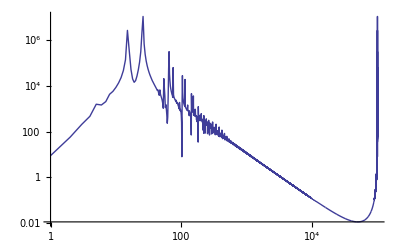

```mathematica
ListLogLogPlot[Abs[Fourier[Table[Evaluate[vz[t] /. %[[1,6]]],{t,0,100,.001}]]]^2,Joined->True,PlotRange->Full]
```

```mathematica
NDSolve[{eqns,x[0]==x0,y[0]==y0,z[0]==z0,vx[0]==vx0,vy[0]==vy0,vz[0]==vz0},{x,y,z,vx,vy,vz},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,MaxSteps->Infinity]
```

```mathematica
Flatten[Append[{1,2,3},{4,5,6}]]
```

{1,2,3,4,5,6}

```mathematica
inits=Table[Range[-1,1]/10.0
```

```mathematica
ϕ=0
```

0

```mathematica
ϕ=Pi/4;dat30=Map[psectz,dat3Inits]; ListPlot[dat30,Frame->True,Axes->False,FrameLabel->{"x","v_x"},PlotLabel->"Z section, ϕ=45"]
dat20=Map[psecty,dat2Inits]; ListPlot[dat20,Frame->True,Axes->False,FrameLabel->{"x","v_x"},PlotLabel->"Y section, ϕ=45"]
```

```mathematica
ListLogLogPlot[Abs[Fourier[Table[Evaluate[vx[t] /. dat3[[1,1]]],{t,0,100,.001}]]]^2,Joined->True]
```

ReplaceAll::reps: {14.3436, 15.9892} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Fourier::fftl: Argument {vx[0.]/. {14.3436, 15.9892}, vx[0.001]/. {14.3436, 15.9892}, vx[0.002]/. {14.3436, 15.9892}, vx[0.003]/. {14.3436, 15.9892}, vx[0.004]/. {14.3436, 15.9892}, vx[0.005]/. {14.3436, 15.9892}, vx[0.006]/. {14.3436, 15.9892}, « 37 », vx[0.044]/. {14.3436, 15.9892}, vx[0.045]/. {14.3436, 15.9892}, vx[0.046]/. {14.3436, 15.9892}, vx[0.047]/. {14.3436, 15.9892}, vx[0.048]/. {14.3436, 15.9892}, vx[0.049]/. {14.3436, 15.9892}, « 99951 »} is not a non-empty list or rectangular array of numeric quantities.

ListLogLogPlot::lpn: Abs[Fourier[{vx[0.]/. {14.3436, 15.9892}, vx[0.001]/. {14.3436, 15.9892}, vx[0.002]/. {14.3436, 15.9892}, vx[0.003]/. {14.3436, 15.9892}, « 44 », vx[0.048]/. {14.3436, 15.9892}, vx[0.049]/. {14.3436, 15.9892}, « 99951 »}]]^2 is not a list of numbers or pairs of numbers.

ListLogLogPlot[Abs[Fourier[{vx[0.]/.{14.3436,15.9892},vx[0.001]/.{14.3436,15.9892},vx[0.002]/.{14.3436,15.9892},«99995»,vx[99.998]/.{14.3436,15.9892},vx[99.999]/.{14.3436,15.9892},vx[100.]/.{14.3436,15.9892}}]]^2,Joined→True]

```mathematica
Range[.1,30.,30./(2^4-1)]
```

{0.1,2.1,4.1,6.1,8.1,10.1,12.1,14.1,16.1,18.1,20.1,22.1,24.1,26.1,28.1}

```mathematica
Length[Range[0,60,60./(2^4-1)]]
```

16

```mathematica
E0=Energy[{-30,0,0,-30,0,-15}]
```

4826.95

```mathematica
inits=Table[{Range[-30,30,60./(2^4-1)][[i]],Range[-30,30,60./(2^4-1)][[j]]},{i,1,2^4},{j,1,2^4}]
```

{{{-30.,-30.},{-30.,-26.},{-30.,-22.},{-30.,-18.},{-30.,-14.},{-30.,-10.},{-30.,-6.},{-30.,-2.},{-30.,2.},{-30.,6.},{-30.,10.},{-30.,14.},{-30.,18.},{-30.,22.},{-30.,26.},{-30.,30.}},{{-26.,-30.},{-26.,-26.},{-26.,-22.},{-26.,-18.},{-26.,-14.},{-26.,-10.},{-26.,-6.},{-26.,-2.},{-26.,2.},{-26.,6.},{-26.,10.},{-26.,14.},{-26.,18.},{-26.,22.},{-26.,26.},{-26.,30.}},{{-22.,-30.},{-22.,-26.},{-22.,-22.},{-22.,-18.},{-22.,-14.},{-22.,-10.},{-22.,-6.},{-22.,-2.},{-22.,2.},{-22.,6.},{-22.,10.},{-22.,14.},{-22.,18.},{-22.,22.},{-22.,26.},{-22.,30.}},{{-18.,-30.},{-18.,-26.},{-18.,-22.},{-18.,-18.},{-18.,-14.},{-18.,-10.},{-18.,-6.},{-18.,-2.},{-18.,2.},{-18.,6.},{-18.,10.},{-18.,14.},{-18.,18.},{-18.,22.},{-18.,26.},{-18.,30.}},{{-14.,-30.},{-14.,-26.},{-14.,-22.},{-14.,-18.},{-14.,-14.},{-14.,-10.},{-14.,-6.},{-14.,-2.},{-14.,2.},{-14.,6.},{-14.,10.},{-14.,14.},{-14.,18.},{-14.,22.},{-14.,26.},{-14.,30.}},{{-10.,-30.},{-10.,-26.},{-10.,-22.},{-10.,-18.},{-10.,-14.},{-10.,-10.},{-10.,-6.},{-10.,-2.},{-10.,2.},{-10.,6.},{-10.,10.},{-10.,14.},{-10.,18.},{-10.,22.},{-10.,26.},{-10.,30.}},{{-6.,-30.},{-6.,-26.},{-6.,-22.},{-6.,-18.},{-6.,-14.},{-6.,-10.},{-6.,-6.},{-6.,-2.},{-6.,2.},{-6.,6.},{-6.,10.},{-6.,14.},{-6.,18.},{-6.,22.},{-6.,26.},{-6.,30.}},{{-2.,-30.},{-2.,-26.},{-2.,-22.},{-2.,-18.},{-2.,-14.},{-2.,-10.},{-2.,-6.},{-2.,-2.},{-2.,2.},{-2.,6.},{-2.,10.},{-2.,14.},{-2.,18.},{-2.,22.},{-2.,26.},{-2.,30.}},{{2.,-30.},{2.,-26.},{2.,-22.},{2.,-18.},{2.,-14.},{2.,-10.},{2.,-6.},{2.,-2.},{2.,2.},{2.,6.},{2.,10.},{2.,14.},{2.,18.},{2.,22.},{2.,26.},{2.,30.}},{{6.,-30.},{6.,-26.},{6.,-22.},{6.,-18.},{6.,-14.},{6.,-10.},{6.,-6.},{6.,-2.},{6.,2.},{6.,6.},{6.,10.},{6.,14.},{6.,18.},{6.,22.},{6.,26.},{6.,30.}},{{10.,-30.},{10.,-26.},{10.,-22.},{10.,-18.},{10.,-14.},{10.,-10.},{10.,-6.},{10.,-2.},{10.,2.},{10.,6.},{10.,10.},{10.,14.},{10.,18.},{10.,22.},{10.,26.},{10.,30.}},{{14.,-30.},{14.,-26.},{14.,-22.},{14.,-18.},{14.,-14.},{14.,-10.},{14.,-6.},{14.,-2.},{14.,2.},{14.,6.},{14.,10.},{14.,14.},{14.,18.},{14.,22.},{14.,26.},{14.,30.}},{{18.,-30.},{18.,-26.},{18.,-22.},{18.,-18.},{18.,-14.},{18.,-10.},{18.,-6.},{18.,-2.},{18.,2.},{18.,6.},{18.,10.},{18.,14.},{18.,18.},{18.,22.},{18.,26.},{18.,30.}},{{22.,-30.},{22.,-26.},{22.,-22.},{22.,-18.},{22.,-14.},{22.,-10.},{22.,-6.},{22.,-2.},{22.,2.},{22.,6.},{22.,10.},{22.,14.},{22.,18.},{22.,22.},{22.,26.},{22.,30.}},{{26.,-30.},{26.,-26.},{26.,-22.},{26.,-18.},{26.,-14.},{26.,-10.},{26.,-6.},{26.,-2.},{26.,2.},{26.,6.},{26.,10.},{26.,14.},{26.,18.},{26.,22.},{26.,26.},{26.,30.}},{{30.,-30.},{30.,-26.},{30.,-22.},{30.,-18.},{30.,-14.},{30.,-10.},{30.,-6.},{30.,-2.},{30.,2.},{30.,6.},{30.,10.},{30.,14.},{30.,18.},{30.,22.},{30.,26.},{30.,30.}}}

```mathematica
ListPlot[inits]
```

```mathematica
xvals=Table[RandomChoice[x/.NSolve[Energy[{inits[[i,j]][[1]],0,0,inits[[i,j]][[2]],0,x}]==E0,x]],{i,1,16},{j,1,16}]
```

{{15.,21.1896,25.318,28.3019,30.4795,32.0156,33.,33.4813,33.4813,-33.,32.0156,-30.4795,28.3019,-25.318,-21.1896,-15.},{24.2719,28.5153,-31.7037,34.1339,-35.96,37.271,-38.1199,38.5373,38.5373,38.1199,-37.271,-35.96,34.1339,31.7037,-28.5153,-24.2719},{-31.6813,35.0386,-37.6789,-39.7455,41.3244,-42.47,-43.2169,-43.5856,-43.5856,-43.2169,-42.47,-41.3244,39.7455,-37.6789,35.0386,-31.6813},{38.4915,41.2988,-43.5614,-45.3607,46.7503,-47.766,48.4313,-48.7606,-48.7606,-48.4313,-47.766,-46.7503,-45.3607,-43.5614,-41.2988,-38.4915},{-45.1595,-47.575,49.5518,51.1408,-52.3773,53.2858,-53.883,54.1792,-54.1792,-53.883,53.2858,52.3773,-51.1408,-49.5518,-47.575,45.1595},{-51.9433,54.0565,-55.8042,-57.2198,58.3276,-59.1448,59.6834,59.9509,-59.9509,-59.6834,59.1448,-58.3276,57.2198,55.8042,54.0565,51.9433},{59.0765,60.9429,62.4982,63.7654,-64.7613,65.4983,-65.9851,-66.2271,-66.2271,65.9851,-65.4983,-64.7613,63.7654,62.4982,-60.9429,59.0765},{-68.2349,-69.857,-71.218,-72.3326,73.212,-73.8648,74.2967,-74.5118,74.5118,-74.2967,-73.8648,-73.212,72.3326,-71.218,69.857,-68.2349},{-68.2349,69.857,71.218,-72.3326,-73.212,73.8648,74.2967,-74.5118,74.5118,-74.2967,73.8648,-73.212,-72.3326,71.218,-69.857,68.2349},{59.0765,-60.9429,62.4982,-63.7654,-64.7613,-65.4983,-65.9851,66.2271,66.2271,-65.9851,-65.4983,64.7613,-63.7654,-62.4982,60.9429,59.0765},{-51.9433,-54.0565,-55.8042,-57.2198,-58.3276,-59.1448,59.6834,-59.9509,59.9509,-59.6834,59.1448,-58.3276,-57.2198,55.8042,54.0565,-51.9433},{45.1595,-47.575,-49.5518,-51.1408,-52.3773,-53.2858,53.883,54.1792,54.1792,53.883,53.2858,-52.3773,-51.1408,49.5518,47.575,45.1595},{-38.4915,-41.2988,43.5614,45.3607,-46.7503,47.766,-48.4313,48.7606,-48.7606,-48.4313,-47.766,46.7503,45.3607,43.5614,41.2988,-38.4915},{-31.6813,35.0386,37.6789,-39.7455,41.3244,42.47,43.2169,-43.5856,43.5856,-43.2169,42.47,41.3244,39.7455,37.6789,35.0386,31.6813},{-24.2719,-28.5153,-31.7037,-34.1339,35.96,-37.271,-38.1199,-38.5373,38.5373,38.1199,37.271,-35.96,34.1339,31.7037,28.5153,24.2719},{15.,21.1896,-25.318,28.3019,30.4795,-32.0156,33.,-33.4813,-33.4813,33.,-32.0156,30.4795,-28.3019,-25.318,21.1896,15.}}

```mathematica
x>0/.{{x->-47.38762896577727},{x->47.38762896577726}}
```

{False,True}

```mathematica
Flatten[Inits2[[{1,2},{1,2}]]]
```

{0.1,0,0,0.1,100.549,0,0.1,0,0,3.85,-100.475,0,1.975,0,0,0.1,-86.3856,0,1.975,0,0,3.85,86.2999,0}

```mathematica
test=Table[Map[psecty,Inits2[[All,i]]],{i,1,3}]
```

{{«1»},«1»,{{{0.193825,-6.56871},{-0.103802,15.0993},{0.703047,-15.0108},{-0.917095,5.83257},{0.477001,-5.13495},{-0.122139,11.8539},{0.455008,-16.3922},{-1.05512,7.60561},{0.752718,-1.10413},{-0.470511,3.67406},{0.0225479,-8.51416},{0.159813,5.48418},{-0.477129,2.27883},{-0.0468035,-2.18607},{-0.292668,3.75938},{-0.0390355,-5.67974},{0.595059,1.37799},«14»,{0.720916,0.477784},{-0.909136,-3.20622},{0.895182,14.7697},{0.00100693,-23.5311},{-0.925354,14.5082},{0.901282,-2.87651},{-0.768538,-0.335938},{1.02739,6.03156},{-0.590118,-16.3145},{0.0569927,15.5502},{-0.0649397,-9.06843},{0.558436,3.82572},{-0.955378,-5.92354},{0.663028,15.4673},{-0.088678,-15.1209},{0.167626,6.77041},{-0.673524,-1.47815}},«15»}}

```mathematica
ListPlot[test[[{1,3}]]]
```

-Graphics-

```mathematica
Inits6=Table[{inits[[i,j]][[1]],0,0,inits[[i,j]][[2]],0,xvals[[i,j]]},{i,1,16},{j,1,16}];
```

```mathematica
dat20=Table[Map[psecty,Inits2[All,i]],{i,1,16}]; ListPlot[dat20[[All,All]],Frame->True,Axes->False,FrameLabel->{"x","v_x"},PlotLabel->"y=0 Section, E=5774.1, ϕ=90, q_1=1.6 , q_2=1.0 , q_z=1.25 "]
dat20lams=Table[LCEsC[F,dat3Inits[[i,j]],.1,100,4],{i,1,16},{j,1,16}];
```

-Graphics-

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

IdentityMatrix::dims: Dimension specification 0 should be a positive machine integer or a pair of positive machine integers.

Set::shape: Lists {x0$338784, V0$338784} and IntVarEq[F[{}], Transpose[{}] . Transpose[JacobianMtx[F[{}], {}]], {}, Transpose[{}], 30.  + 4.\ F[{}], IdentityMatrix[0], {0.1, 0.02}] are not the same shape.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Set::shape: Lists {x0$338784, V0$338784} and IntVarEq[F[{}], Transpose[{}] . Transpose[JacobianMtx[F[{}], {}]], {}, Transpose[{}], 30.  + 4.\ F[{}], {Indeterminate}, {0.1, 0.02}] are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Last::nolast: {} has a length of zero and no last element.

Part::pspec: Part specification Last[{}] is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification 1 + Last[{}] is neither a machine-sized integer nor a list of machine-sized integers.

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

IdentityMatrix::dims: Dimension specification 0 should be a positive machine integer or a pair of positive machine integers.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Last::nolast: {} has a length of zero and no last element.

Part::pspec: Part specification Last[{}] is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

IdentityMatrix::dims: Dimension specification 0 should be a positive machine integer or a pair of positive machine integers.

General::stop: Further output of IdentityMatrix :: dims will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Last::nolast: {} has a length of zero and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

Part::partw: Part 7 of {30, 0, 0, -5, 0, 10} does not exist.

Part::partw: Part 7 of {30., 0., 0., -5., 0., 10.} does not exist.

$Aborted

```mathematica
dat20[[254]]
```

{{-57.4705,-8.52088},{-1.47445,87.8267},{-19.6304,-60.4204},{-25.0312,53.0639},{55.8378,6.16735},{-25.6324,-51.1435},{-12.2116,68.9573},{53.9581,13.5121},{-19.2078,-58.1008},{-9.9451,70.8602},{57.3521,-5.93724},{11.8671,-71.8636},{42.483,32.4074},{6.38928,-77.8092},{27.1277,51.9772},{25.1341,-54.9032},{17.1154,64.7061},{35.7526,-40.5898},{-54.6474,-5.22996},{36.3746,38.1615},{-2.20972,-79.5354},{0.751859,78.8276},{-21.9669,-43.7784},{47.0683,12.7867},{-23.6029,37.7965},{-6.44581,-53.4169},{35.8923,-24.4232},{-0.0881973,79.2478},{-25.8134,-38.2829},{50.4124,3.24614},{-26.4332,36.626},{-1.67388,-61.6213},{45.5165,-6.18741},{-1.85381,64.6059},{-19.4567,-45.978},{47.7356,10.1301},{-21.3321,40.7796},{-6.70546,-54.3328},{40.3304,-18.7737},{-3.09343,65.9709},{-11.4256,-56.7315},{40.8113,20.8256},{-22.3516,38.6072},{-7.85086,-51.382},{33.227,-27.9177},{0.513408,64.4698},{-44.0359,9.75404},{0.507966,-70.5829},{21.9956,43.1962},{-48.3998,-9.43931},{23.3995,-38.685},{5.46478,55.5475},{-40.8122,17.7454},{2.61831,-66.3753},{12.3173,55.6338},{-41.2296,-20.4219},{25.1504,-36.0469},{5.83722,53.7021},{-34.9818,25.3476}}

```mathematica
dat20=Map[psecty,Inits3];ListPlot[dat20,Frame->True,Axes->False,AxesLabel->{"x","v_x"}]
```

Part::partw: Part 1 of {} does not exist.

```mathematica
ListPlot[dat20]
```

```mathematica
Inits7=Inits6[[All,1]];
```

```mathematica
For[i=2,i≤16,i++,Inits7=Join[Inits7,Inits6[[All,i]]]]
```

```mathematica
Length[Inits7]
```

256

```mathematica
dat7lams=Table[LCEsC[F,Inits6[[2*i,2*j]],.1,100,4],{i,1,8},{j,1,8}]
```

LCE::pos: The sum of the LCEs must be less than or equal to zero.

General::stop: Further output of LCE :: pos will be suppressed during this calculation.

{{{{0.260114,0.108342,0.0910773,-0.0910773,-0.103509,-0.264948},6.},{{0.246587,0.100973,0.0955158,-0.0738451,-0.100973,-0.268258},6.},{{0.211145,0.107992,0.100274,-0.0463412,-0.100274,-0.272796},6.},{{0.19724,0.116152,0.0906704,-0.0320005,-0.0906704,-0.281391},6.},{{0.163493,0.149721,0.0768704,-0.0311388,-0.0768704,-0.282076},6.},{{0.240478,0.0767978,0.0717035,-0.0443889,-0.0717035,-0.272887},6.},{{0.270708,0.0884927,0.0483763,-0.0734699,-0.0884927,-0.245614},6.},{{0.282354,0.135147,0.0429791,-0.107813,-0.135147,-0.217521},6.}},{{{0.312835,0.303194,0.130807,-0.157774,-0.285868,-0.303194},6.},{{0.356854,0.320067,0.143412,-0.148842,-0.314638,-0.356854},6.},{{0.402662,0.298332,0.221505,-0.163432,-0.356411,-0.402662},5.99999},{{0.409959,0.322971,0.206078,-0.190859,-0.338207,-0.409961},5.99995},{{0.348464,0.318081,0.200422,-0.18907,-0.329442,-0.348465},5.99997},{{0.316954,0.236493,0.0968991,-0.163464,-0.236493,-0.25039},6.},{{0.313164,0.12029,0.0528465,-0.12029,-0.17942,-0.18659},6.},{{0.324495,0.0359981,0.0325959,-0.0359981,-0.120798,-0.236293},6.}},{{{0.37699,0.20396,-0.00323836,-0.0805594,-0.120166,-0.37699},5.99999},{{0.359525,0.242753,-0.0201653,-0.0289126,-0.193675,-0.359525},6.},{{0.470863,0.366644,0.11261,-0.0538933,-0.366644,-0.529581},6.},{{0.406799,0.312508,0.117194,-0.0638668,-0.312508,-0.460126},6.},{{0.530394,0.327394,0.0766604,-0.018374,-0.327394,-0.588683},6.},{{0.355043,0.354795,0.0913313,-0.0515297,-0.355044,-0.394606},5.99997},{{0.428947,0.367223,0.0711491,-0.0855062,-0.367231,-0.414669},5.99979},{{0.671531,0.417154,0.101407,-0.112943,-0.417536,-0.65955},$Failed}},{{{0.694689,0.515318,0.0360217,-0.0670681,-0.51532,-0.663677},5.99994},{{0.876746,0.706162,0.431501,-0.313486,-0.707049,-0.995656},5.99821},{{0.684035,0.431385,0.389904,-0.240195,-0.579241,-0.685013},$Failed},{{0.732961,0.653834,0.0546201,-0.050722,-0.653846,-0.736973},5.99983},{{0.774553,0.693915,0.106238,-0.0511051,-0.69405,-0.830027},5.99943},{{1.24226,0.755675,0.149081,-0.51259,-0.756644,-0.877257},$Failed},{{0.748775,0.513493,0.167186,-0.249804,-0.514147,-0.665248},$Failed},{{0.377534,0.269335,0.0359779,-0.109155,-0.196172,-0.377535},5.99996}},{{{0.314326,0.164736,-0.0146219,-0.0370501,-0.113064,-0.314326},6.},{{0.389295,0.349926,0.0170848,-0.0478555,-0.349926,-0.358526},6.},{{0.43512,0.399658,0.04126,-0.0539868,-0.399658,-0.422397},5.99999},{{0.512048,0.491702,0.126204,-0.134875,-0.491703,-0.503396},5.99996},{{0.746071,0.502516,0.41753,-0.321215,-0.599226,-0.746774},5.99853},{{0.50756,0.25923,0.0512456,-0.127426,-0.183065,-0.507561},5.99997},{{0.489781,0.4206,0.0374678,-0.0597726,-0.4206,-0.467479},5.99999},{{0.441808,0.387512,-0.0197272,-0.118498,-0.303585,-0.387512},5.99999}},{{{1.78394,1.20043,0.96719,-0.973577,-1.20738,-1.77768},5.99602},{{0.363977,0.21551,0.0932501,-0.21551,-0.216302,-0.240927},5.99999},{{0.276185,0.223666,0.109527,-0.141926,-0.223666,-0.243786},6.},{{0.267406,0.193237,0.174732,-0.111217,-0.256752,-0.267406},6.},{{0.322894,0.142242,0.0736068,-0.104965,-0.110885,-0.322894},6.},{{0.4544,0.38264,0.106369,-0.081776,-0.382641,-0.479004},5.99998},{{1.39459,0.983122,0.448064,-0.494219,-0.990617,-1.34257},5.99878},{{0.641133,0.585617,0.22768,-0.279102,-0.585694,-0.589889},5.99957}},{{{0.293749,0.0653143,0.0378307,-0.0653143,-0.151738,-0.179842},6.},{{0.288064,0.0825627,0.0484315,-0.0825627,-0.108161,-0.228335},6.},{{0.269376,0.127537,0.0954005,-0.08845,-0.127537,-0.276327},6.},{{0.215579,0.181775,0.175011,-0.081943,-0.175011,-0.315411},6.},{{0.203258,0.19995,0.198494,-0.085516,-0.203258,-0.312927},6.},{{0.263251,0.20681,0.127026,-0.0982374,-0.20681,-0.292039},6.},{{0.272986,0.192611,0.118967,-0.118718,-0.192611,-0.273236},6.},{{0.282261,0.167788,0.132508,-0.141627,-0.167788,-0.273142},6.}},{{{0.22103,0.1629,0.0235773,0.0152784,-0.1629,-0.259886},6.},{{0.187529,0.0945042,0.0816728,0.000998896,-0.0945042,-0.2702},6.},{{0.184083,0.0945898,0.0502697,-0.00287317,-0.0502697,-0.275799},6.},{{0.186025,0.0941377,0.0225244,-0.00524012,-0.0225244,-0.274923},6.},{{0.184883,0.098387,0.00794214,-0.00794214,-0.015842,-0.267428},6.},{{0.221604,0.0748456,0.00392634,-0.00392634,-0.0344359,-0.262014},6.},{{0.244284,0.0789255,0.00497582,-0.00497582,-0.0633169,-0.259892},6.},{{0.272486,0.0386028,0.000385019,-0.00038502,-0.0592055,-0.251883},6.}}}

```mathematica
dat5b=Map[psecty,Inits5];ListPlot[dat5b,Frame->True,Axes->False,PlotRange->Full,FrameLabel->{"x","v_x"},PlotLabel->"y=0 Section of Surface for E=4826.95"]
```

```mathematica
dat7b=Map[psectz,Inits7];ListPlot[dat7b,Frame->True,Axes->False,PlotRange->Full,FrameLabel->{"x","v_x"},PlotLabel->"z=0 Section of Surface for E=4826.95"]
```

```mathematica
Table[Energy[Inits7[[i]]], {i,1,3}]
```

{5640.57,5614.96,5589.41}

```mathematica
dat7lamplotsmat1=Table[{Inits6[[2*i,2*j]][[1]],Inits6[[2*i,2*j]][[4]],First[dat7lams[[i,j]]][[1]]},{i,1,8},{j,1,8}]
```

{{{-26.,-26.,0.260114},{-26.,-18.,0.246587},{-26.,-10.,0.211145},{-26.,-2.,0.19724},{-26.,6.,0.163493},{-26.,14.,0.240478},{-26.,22.,0.270708},{-26.,30.,0.282354}},{{-18.,-26.,0.312835},{-18.,-18.,0.356854},{-18.,-10.,0.402662},{-18.,-2.,0.409959},{-18.,6.,0.348464},{-18.,14.,0.316954},{-18.,22.,0.313164},{-18.,30.,0.324495}},{{-10.,-26.,0.37699},{-10.,-18.,0.359525},{-10.,-10.,0.470863},{-10.,-2.,0.406799},{-10.,6.,0.530394},{-10.,14.,0.355043},{-10.,22.,0.428947},{-10.,30.,0.671531}},{{-2.,-26.,0.694689},{-2.,-18.,0.876746},{-2.,-10.,0.684035},{-2.,-2.,0.732961},{-2.,6.,0.774553},{-2.,14.,1.24226},{-2.,22.,0.748775},{-2.,30.,0.377534}},{{6.,-26.,0.314326},{6.,-18.,0.389295},{6.,-10.,0.43512},{6.,-2.,0.512048},{6.,6.,0.746071},{6.,14.,0.50756},{6.,22.,0.489781},{6.,30.,0.441808}},{{14.,-26.,1.78394},{14.,-18.,0.363977},{14.,-10.,0.276185},{14.,-2.,0.267406},{14.,6.,0.322894},{14.,14.,0.4544},{14.,22.,1.39459},{14.,30.,0.641133}},{{22.,-26.,0.293749},{22.,-18.,0.288064},{22.,-10.,0.269376},{22.,-2.,0.215579},{22.,6.,0.203258},{22.,14.,0.263251},{22.,22.,0.272986},{22.,30.,0.282261}},{{30.,-26.,0.22103},{30.,-18.,0.187529},{30.,-10.,0.184083},{30.,-2.,0.186025},{30.,6.,0.184883},{30.,14.,0.221604},{30.,22.,0.244284},{30.,30.,0.272486}}}

```mathematica
dat7lamplots1=dat7lamplotsmat1[[All,1]]
```

{{-26.,-26.,0.260114},{-18.,-26.,0.312835},{-10.,-26.,0.37699},{-2.,-26.,0.694689},{6.,-26.,0.314326},{14.,-26.,1.78394},{22.,-26.,0.293749},{30.,-26.,0.22103}}

```mathematica
For[i=2,i≤8,i++,dat7lamplots1=Join[dat7lamplots1,dat7lamplotsmat1[[All,i]]]];
```

```mathematica
ListContourPlot[dat7lamplots,Frame->True,Axes->False,FrameLabel->{"x","v_x"},PlotLabel->"Norm of the Lyapunov Exponents for E=4826.95",Contours->32,ContourLabels->All]
```

```mathematica
ListDensityPlot[dat7lamplots,Frame->True,Axes->False,FrameLabel->{"x","v_x"},PlotLabel->"Density Plot of √(∑_i)  for E=4826.95",ColorFunction->GrayLevel]
```

```mathematica
ListContourPlot[dat7lamplots1,Frame->True,Axes->False,FrameLabel->{"x","v_x"},PlotLabel->"Density Plot of the Largest Lyapunov Exponent for E=4826.95"]
```

```mathematica
ListPlot[Inits5,Frame->True,Axes->False,FrameLabel->{"x","v_x"}]
```

```mathematica
E0
```

4826.95